```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
ρmin=0.;
ρmax=30000.;
c0=1.85*10^6;
fpi=93.5;
cmax=10.^7;
cmin=10.^-2;
rhoend=500.;
```

## mub=0

```mathematica
lT=50;
T=Table[Exp[Log[10^-4]-(Log[10^-4]-Log[100])/lT*(i-1)]//N,{i,1,lT}];
alist=Table[Flatten[Import["./mub0_IR0p01/bdata/b"<>ToString[i]<>".dat"]],{i,1,lT}];
alist1=Table[Rest[alist[[i]]],{i,1,lT}];
```

Import::nffil: 在 Import 期间没有找到文件 ./mub0_IR0p01/bdata/b21.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./mub0_IR0p01/bdata/b22.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./mub0_IR0p01/bdata/b23.dat.

General::stop: 在本次计算中，Import::nffil 的进一步输出将被抑制.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

Flatten::argb: 调用 Flatten 时使用了 0 个参数；应该用 1 到 3 个参数.

General::stop: 在本次计算中，Flatten::argb 的进一步输出将被抑制.

```mathematica
V1mub0=Flatten[Transpose[Table[Flatten[Import["./mub0/dVd1rdata/dvdr"<>ToString[i]<>".dat"]],{i,1,lT}]]];
driv1mub0=Table[Re[SetPrecision[Sum[alist1[[i]][[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,50}]+1/2 First[alist[[i]]],100]/.{ρ->0}],{i,1,lT}];
slopmub0=Table[{SetPrecision[(T[[i]])/125.92641,90],SetPrecision[FindFit[Transpose[{-Log[T/125.92641],Log[1/√driv1mub0]}][[i-1;;i+1]],a x+b,{a,b},x][[1]][[2]],90]},{i,2,lT-1}];
```

Import::nffil: 在 Import 期间没有找到文件 ./mub0/dVd1rdata/dvdr1.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./mub0/dVd1rdata/dvdr2.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./mub0/dVd1rdata/dvdr3.dat.

General::stop: 在本次计算中，Import::nffil 的进一步输出将被抑制.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

Part::partw: Flatten[] 的部分 1 不存在.

Part::partw: Flatten[] 的部分 2 不存在.

Part::partw: Flatten[] 的部分 3 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

```mathematica
Export["./numub0.dat",slopmub0];
```

```mathematica
Length[V1mub0]
```

50

```mathematica
Length[T]
```

50

```mathematica
ListPlot[Transpose[{T,V1mub0}],PlotRange->All,ScalingFunctions->{"Log","Log"}]
```

-Graphics-

## mub=600

```mathematica
lT=20;
T=Table[Exp[Log[10^-3]-(Log[10^-3]-Log[100])/lT*(i-1)]//N,{i,1,lT}];
alist=Table[Flatten[Import["./mub600/bdata/b"<>ToString[i]<>".dat"]],{i,1,lT}];
alist1=Table[Rest[alist[[i]]],{i,1,lT}];
```

Import::nffil: 在 Import 期间没有找到文件 ./mub600/bdata/b1.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./mub600/bdata/b2.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./mub600/bdata/b3.dat.

General::stop: 在本次计算中，Import::nffil 的进一步输出将被抑制.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

Flatten::argb: 调用 Flatten 时使用了 0 个参数；应该用 1 到 3 个参数.

General::stop: 在本次计算中，Flatten::argb 的进一步输出将被抑制.

```mathematica
V1mub600=Flatten[Transpose[Table[Flatten[Import["./mub600/dVd1rdata/dvdr"<>ToString[i]<>".dat"]],{i,1,lT}]]];
driv1mub600=Table[Re[SetPrecision[Sum[alist1[[i]][[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,50}]+1/2 First[alist[[i]]],100]/.{ρ->0}],{i,1,lT}];
slopmub600=Table[{SetPrecision[T[[i]]/80.9044,90],SetPrecision[FindFit[Transpose[{-Log[T/80.9044],Log[1/√driv1mub600]}][[i-1;;i+1]],a x+b,{a,b},x][[1]][[2]],90]},{i,2,lT-1}];
```

Import::nffil: 在 Import 期间没有找到文件 ./mub600/dVd1rdata/dvdr1.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./mub600/dVd1rdata/dvdr2.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./mub600/dVd1rdata/dvdr3.dat.

General::stop: 在本次计算中，Import::nffil 的进一步输出将被抑制.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

Part::partw: Flatten[] 的部分 1 不存在.

Part::partw: Flatten[] 的部分 2 不存在.

Part::partw: Flatten[] 的部分 3 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

```mathematica
Export["./numub600.dat",slopmub600];
```

## mub=650

```mathematica
lT=20;
T=Table[Exp[Log[10^-3]-(Log[10^-3]-Log[100])/lT*(i-1)]//N,{i,1,lT}];
alist=Table[Flatten[Import["./mub650/bdata/b"<>ToString[i]<>".dat"]],{i,1,lT}];
alist1=Table[Rest[alist[[i]]],{i,1,lT}];
```

Import::nffil: 在 Import 期间没有找到文件 ./mub650/bdata/b1.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./mub650/bdata/b2.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./mub650/bdata/b3.dat.

General::stop: 在本次计算中，Import::nffil 的进一步输出将被抑制.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

Flatten::argb: 调用 Flatten 时使用了 0 个参数；应该用 1 到 3 个参数.

General::stop: 在本次计算中，Flatten::argb 的进一步输出将被抑制.

```mathematica
V1mub650=Flatten[Transpose[Table[Flatten[Import["./mub650/dVd1rdata/dvdr"<>ToString[i]<>".dat"]],{i,1,lT}]]];
driv1mub650=Table[Re[SetPrecision[Sum[alist1[[i]][[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,50}]+1/2 First[alist[[i]]],100]/.{ρ->0}],{i,1,lT}];
slopmub650=Table[{SetPrecision[T[[i]]/69.94333,90],SetPrecision[FindFit[Transpose[{-Log[T/69.94333],Log[1/√driv1mub650]}][[i-1;;i+1]],a x+b,{a,b},x][[1]][[2]],90]},{i,2,lT-1}];
```

Import::nffil: 在 Import 期间没有找到文件 ./mub650/dVd1rdata/dvdr1.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./mub650/dVd1rdata/dvdr2.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./mub650/dVd1rdata/dvdr3.dat.

General::stop: 在本次计算中，Import::nffil 的进一步输出将被抑制.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

Part::partw: Flatten[] 的部分 1 不存在.

Part::partw: Flatten[] 的部分 2 不存在.

Part::partw: Flatten[] 的部分 3 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

```mathematica
Export["./numub650.dat",slopmub650];
```

## mub=700

```mathematica
lT=20;
T=Table[Exp[Log[10^-3]-(Log[10^-3]-Log[100])/lT*(i-1)]//N,{i,1,lT}];
alist=Table[Flatten[Import["./mub700/bdata/b"<>ToString[i]<>".dat"]],{i,1,lT}];
alist1=Table[Rest[alist[[i]]],{i,1,lT}];
```

Import::nffil: 在 Import 期间没有找到文件 ./mub700/bdata/b1.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./mub700/bdata/b2.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./mub700/bdata/b3.dat.

General::stop: 在本次计算中，Import::nffil 的进一步输出将被抑制.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

Flatten::argb: 调用 Flatten 时使用了 0 个参数；应该用 1 到 3 个参数.

General::stop: 在本次计算中，Flatten::argb 的进一步输出将被抑制.

```mathematica
V1mub700=Flatten[Transpose[Table[Flatten[Import["./mub700/dVd1rdata/dvdr"<>ToString[i]<>".dat"]],{i,1,lT}]]];
driv1mub700=Table[Re[SetPrecision[Sum[alist1[[i]][[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,50}]+1/2 First[alist[[i]]],100]/.{ρ->0}],{i,1,lT}];
slopmub700=Table[{SetPrecision[T[[i]]/55.09038,90],SetPrecision[FindFit[Transpose[{-Log[T/55.09038],Log[1/√driv1mub700]}][[i-1;;i+1]],a x+b,{a,b},x][[1]][[2]],90]},{i,2,lT-1}];
```

Import::nffil: 在 Import 期间没有找到文件 ./mub700/dVd1rdata/dvdr1.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./mub700/dVd1rdata/dvdr2.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./mub700/dVd1rdata/dvdr3.dat.

General::stop: 在本次计算中，Import::nffil 的进一步输出将被抑制.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

Part::partw: Flatten[] 的部分 1 不存在.

Part::partw: Flatten[] 的部分 2 不存在.

Part::partw: Flatten[] 的部分 3 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

```mathematica
Export["./numub700.dat",slopmub700];
```

## mub=TCP

```mathematica
lT=100;
T=Table[Exp[Log[10^-4]-(Log[10^-4]-Log[100])/100*(i-1)]//N,{i,1,lT}];
alist=Table[Flatten[Import["./CP/bdata/b"<>ToString[i]<>".dat"]],{i,1,lT}];
alist1=Table[Rest[alist[[i]]],{i,1,lT}];
```

Import::nffil: 在 Import 期间没有找到文件 ./CP/bdata/b1.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./CP/bdata/b2.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./CP/bdata/b3.dat.

General::stop: 在本次计算中，Import::nffil 的进一步输出将被抑制.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

Flatten::argb: 调用 Flatten 时使用了 0 个参数；应该用 1 到 3 个参数.

General::stop: 在本次计算中，Flatten::argb 的进一步输出将被抑制.

```mathematica
V1TCP=Flatten[Transpose[Table[Flatten[Import["./CP/dVd1rdata/dvdr"<>ToString[i]<>".dat"]],{i,1,lT}]]];
driv1TCP=Table[Re[SetPrecision[Sum[alist1[[i]][[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,50}]+1/2 First[alist[[i]]],100]/.{ρ->0}],{i,1,lT}];
slopTCP=Table[{SetPrecision[T[[i]]/50.858971,90],SetPrecision[FindFit[Transpose[{-Log[T/50.858971],Log[1/√driv1TCP]}][[i-1;;i+1]],a x+b,{a,b},x][[1]][[2]],90]},{i,2,lT-1}];
```

Import::nffil: 在 Import 期间没有找到文件 ./CP/dVd1rdata/dvdr1.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./CP/dVd1rdata/dvdr2.dat.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

Import::nffil: 在 Import 期间没有找到文件 ./CP/dVd1rdata/dvdr3.dat.

General::stop: 在本次计算中，Import::nffil 的进一步输出将被抑制.

Flatten::normal: Flatten[$Failed] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

Part::partw: Flatten[] 的部分 1 不存在.

Part::partw: Flatten[] 的部分 2 不存在.

Part::partw: Flatten[] 的部分 3 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

```mathematica
Export["./nuTCP.dat",slopTCP];
```

## Plot

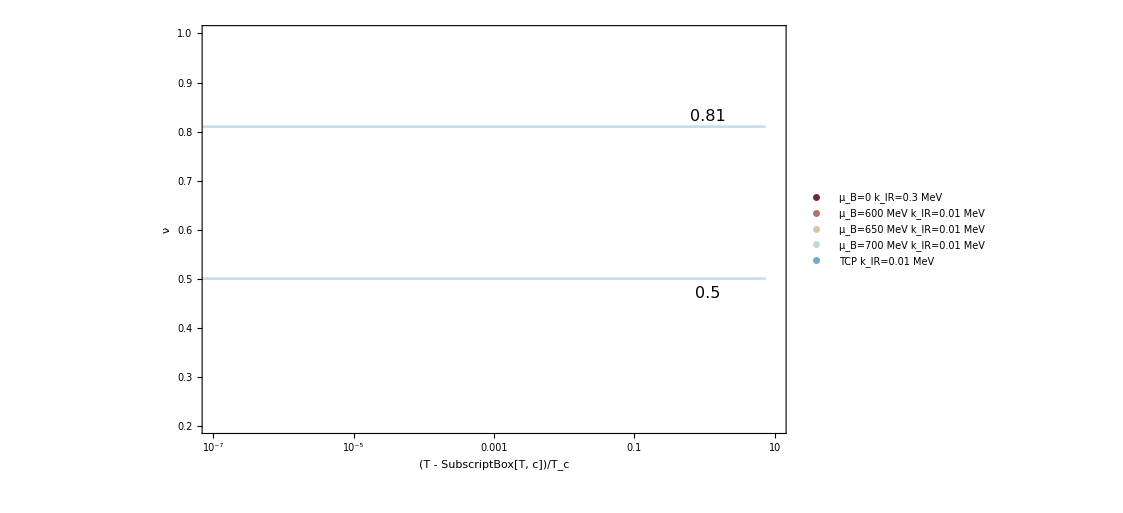

```mathematica
Show[ListPlot[{slopmub0,slopmub600,slopmub650,slopmub700,slopTCP},ScalingFunctions->{"Log",Automatic},
Frame->True,FrameLabel->{Style["(T - SubscriptBox[T, c])/T_c",25,FontFamily->"Times",Black],Style["ν",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.2}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=0 k_IR=0.3 MeV","μ_B=600 MeV k_IR=0.01 MeV","μ_B=650 MeV k_IR=0.01 MeV","μ_B=700 MeV k_IR=0.01 MeV","TCP k_IR=0.01 MeV"},LabelStyle->16],{0.2,0.6}],
PlotRange->{{10^-7,10},{0.2,1.}},AxesOrigin->{10^-7,0.2},FrameTicksStyle->Directive[15,Black],Epilog->{Text[Style["0.5",16],{0.1,0.47}],Text[Style["0.81",16],{0.1,0.83}]}],ListLinePlot[{{-20,0.5},{2,0.5}},PlotStyle->Opacity[0.3]],ListLinePlot[{{-20,0.81},{2,0.81}},PlotStyle->Opacity[0.3]]]
```